```mathematica
?DynamicModule
```

RowBox[{"DynamicModule", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["expr", "TI"]}], "]"}] represents an object which maintains the same local instance of the symbols StyleBox["x", "TI"], StyleBox["y", "TI"], … in the course of all evaluations of Dynamic objects in StyleBox["expr", "TI"]. Symbols specified in a DynamicModule will by default have their values maintained even across StyleBox["Wolfram System", "RebrandingTerm"] sessions. 
RowBox[{"DynamicModule", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], ",", RowBox[{StyleBox["y", "TI"], "=", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["expr", "TI"]}], "]"}] specifies initial values for StyleBox["x", "TI"], StyleBox["y", "TI"], ….

```mathematica
Dynamic[x^2]
```

```mathematica
Slider[0.5]
```

```mathematica
<< FondamentiDiProbabilita.m
```

```mathematica
?PlotLancioDado
```

HistogramRollDice[n] disegna un istogramma per n prove ripetute del lancio di un dado.

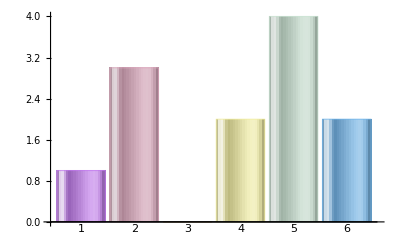

```mathematica
PlotLancioDado[12]
```

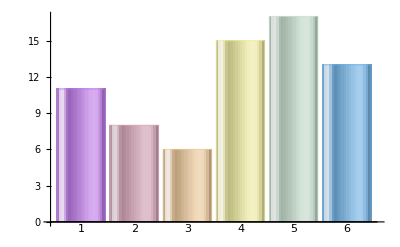

```mathematica
PlotLancioDado[70]
```

```mathematica
PlotLancioDado[-7]
```

PlotLancioDado[-7]

```mathematica
?LancioDado
```

RollDice[] simula il lancio di un dado, restituendo un valore compreso fra 0 e 6.
RollDice[n] simula n volte il lancio di un dado, restituendo una lista di valori compresi fra 0 e 6.

```mathematica
LancioDado[25]
```

{3,3,1,6,1,1,3,4,3,4,5,3,1,3,3,2,1,6,1,2,5,2,6,6,5}

```mathematica
CalcolaSomma[eventi_/;ListQ[eventi],listaDiEventi_/;ListQ[listaDiEventi]]:= 1;
```

```mathematica
CalcolaSomma[{1,2,3},{{1,2,3},{3,4,5},{3,4,5}}]
```

1

```mathematica
?Subset
```

Subset[x,y,…] displays as x⊂y⊂….

```mathematica
Subset[{1,2,3},{1,2,3,4,5,6}]
```

{1,2,3}⊂{1,2,3,4,5,6}

```mathematica
?Subsets
```

Subsets[list] gives a list of all possible subsets of list. 
Subsets[list,n] gives all subsets containing at most n elements. 
Subsets[list,{n}] gives all subsets containing exactly n elements. 
Subsets[list,{n_min,n_max}] gives all subsets containing between n_min and n_max elements. 
Subsets[list,nspec,s] limits the result to the first s subsets. 
Subsets[list,nspec,{s}] gives if possible the s^th subset.

```mathematica
?SubsetQ
```

SubsetQ[list_1,list_2] yields True if list_2 is a subset of list_1, and False otherwise.

```mathematica
SubsetQ[{1,2,3,4,5,6},{1,2,3}]
```

True

```mathematica
?Length
```

RowBox[{"Length", "[", StyleBox["expr", "TI"], "]"}] gives the number of elements in StyleBox["expr", "TI"].

```mathematica
Length[{1,{2,3},{1,2,3}}]
```

3

```mathematica
?Return
```

Return[expr] returns the value expr from a function. 
Return[] returns the value Null.

```mathematica
P[E1 + E2 + E3 + E4 + E5 + E6] /. Plus -> Pippo
```

P[Pippo[E1,E2,E3,E4,E5,E6]]

```mathematica
?ReplacePart
```

ReplacePart[expr,i→new] yields an expression in which the i^th part of expr is replaced by new. 
ReplacePart[expr,{i_1→new_1,i_2→new_2,…}] replaces parts at positions i_n by new_n. 
ReplacePart[expr,{i,j,…}→new] replaces the part at position {i,j,…}. 
ReplacePart[expr,{{i_1,j_1,…}→new_1,…}] replaces parts at positions {i_n,j_n,…} by new_n. 
ReplacePart[expr,{{i_1,j_1,…},…}→new] replaces all parts at positions {i_n,j_n,…} by new. 
ReplacePart[i→new] represents an operator form of ReplacePart that can be applied to an expression.

```mathematica
?Replace
```

Replace[expr,rules] applies a rule or list of rules in an attempt to transform the entire expression expr. 
Replace[expr,rules,levelspec] applies rules to parts of expr specified by levelspec. 
Replace[rules] represents an operator form of Replace that can be applied to an expression.

```mathematica
?Rule
```

RowBox[{StyleBox["lhs", "TI"], "->", StyleBox["rhs", "TI"]}] or RowBox[{StyleBox["lhs", "TI"], "→", StyleBox["rhs", "TI"]}] represents a rule that transforms StyleBox["lhs", "TI"] to StyleBox["rhs", "TI"].

```mathematica
?Probability
```

Probability[pred,x\[Distributed]dist] gives the probability for an event that satisfies the predicate pred under the assumption that x follows the probability distribution dist.
Probability[pred,x\[Distributed]data] gives the probability for an event that satisfies the predicate pred under the assumption that x follows the probability distribution given by data.
Probability[pred,{x_1,x_2,…}\[Distributed]dist] gives the probability that an event satisfies pred under the assumption that {x_1,x_2,…} follows the multivariate distribution dist.
Probability[pred,{x_1\[Distributed]dist_1,x_2\[Distributed]dist_2,…}] gives the probability that an event satisfies pred under the assumption that x_1, x_2, … are independent and follow the distributions dist_1, dist_2, ….
Probability[pred_1\[Conditioned]pred_2,…] gives the conditional probability of pred_1 given pred_2.

```mathematica
?ProbabilityPlot
```

ProbabilityPlot[list] generates a plot of the CDF of list against the CDF of a normal distribution.
ProbabilityPlot[dist] generates a plot of the CDF of the distribution dist against the CDF of a normal distribution.
ProbabilityPlot[data,rdata] generates a plot of the CDF of data against the CDF of rdata.
ProbabilityPlot[data,rdist] generates a plot of the CDF of data against the CDF of symbolic distribution rdist.
ProbabilityPlot[{data_1,data_2,…},ref] generates a plot of the CDF of data_i against the CDF of a reference distribution ref.

```mathematica
?ProbabilityDistribution
```

ProbabilityDistribution[pdf,{x,x_min,x_max}] represents the continuous distribution with PDF pdf in the variable x where the pdf is taken to be zero for x<x_min and x>x_max.
ProbabilityDistribution[pdf,{x,x_min,x_max,dx}] represents the discrete distribution with PDF pdf in the variable x where the pdf is taken to be zero for x<x_min and x>x_max.
ProbabilityDistribution[pdf,{x,…},{y,…},…] represents a multivariate distribution with PDF pdf in the variables x, y, …, etc. 
ProbabilityDistribution[{CDF,cdf},…] represents a probability distribution with CDF given by cdf. 
ProbabilityDistribution[{SF,sf},…] represents a probability distribution with survival function given by sf. 
ProbabilityDistribution[{HF,hf},…] represents a probability distribution with hazard function given by hf.

```mathematica
?ProbabilityScalePlot
```

RowBox[{"ProbabilityScalePlot", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] generates a normal probability plot of the samples SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"ProbabilityScalePlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["\"\!\(\*StyleBox[\"dist\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] generates a probability plot scaled for the distribution "
StyleBox["dist", "TI"]".
RowBox[{"ProbabilityScalePlot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["\"\!\(\*StyleBox[\"dist\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] generates several scaled probability plots for SubscriptBox[StyleBox["data", "TI"], StyleBox["1", "TR"]], SubscriptBox[StyleBox["data", "TI"], StyleBox["2", "TR"]], ….

```mathematica
t = Subsets[{x,y,z}] ;
Delete[t,1]
```

{{x},{y},{z},{x,y},{x,z},{y,z},{x,y,z}}

```mathematica
?First
```

First[expr] gives the first element in expr. 
First[expr,def] gives the first element if it exists, or def otherwise.

```mathematica
Clear[t]
```

```mathematica
CalcolaSommaEventi[listaDiEventi_?ListQ ]:= 
Module[{comb},
comb = Subsets[listaDiEventi];
Delete[comb,1]
];
```

```mathematica
Clear[CalcolaSommaEventi]
```

```mathematica
CalcolaSommaEventi[{1,2,3}] // FullForm
```

List[List[1],List[2],List[3],List[1,2],List[1,3],List[2,3],List[1,2,3]]

```mathematica
comb = Subsets[{1,2,3}];
Delete[comb,1]
```

{{1},{2},{3},{1,2},{1,3},{2,3},{1,2,3}}

```mathematica
Plus[4]
```

4

```mathematica
CalcolaSommaEventi[{e1,e2,e3}]
```

{{e1},{e2},{e3},{e1,e2},{e1,e3},{e2,e3},{e1,e2,e3}}

```mathematica
?/.
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr. 
ReplaceAll[rules] represents an operator form of ReplaceAll that can be applied to an expression.

```mathematica
prova = {{4,5},{6}};
```

```mathematica
Map[f,prova]
```

```mathematica
prova = {f[{4,5}],f[{6}]}
```

{f[{4,5}],f[{6}]}

```mathematica
Replace[prova, x_ /; EvenQ[Length[x]] ->  Apply[Plus,x], 1 ]
```

{f[{4,5}],f[{6}]}

```mathematica
Cases[{{1},{1,2}, {3,4,5},{4,5,6,7}},x_ /; EvenQ[Length[x]]]
```

{{1,2},{4,5,6,7}}

```mathematica
?Replace
```

RowBox[{"Replace", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"]}], "]"}] applies a rule or list of rules in an attempt to transform the entire expression StyleBox["expr", "TI"]. 
RowBox[{"Replace", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies rules to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Replace", "[", StyleBox["rules", "TI"], "]"}] represents an operator form of Replace that can be applied to an expression.

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,{1}] or f@@@expr replaces heads at level 1 of expr by f.
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec. 
Apply[f] represents an operator form of Apply that can be applied to an expression.

```mathematica
Apply[Plus,{{1,2},{3}},2]
```

{3,3}

```mathematica
ClearAll
```

ClearAll

```mathematica
provina = {{1},{2},{1,2},{3,4,5},{2,3,1,4}};
```

```mathematica
?ReplacePart
```

ReplacePart[expr,i→new] yields an expression in which the i^th part of expr is replaced by new. 
ReplacePart[expr,{i_1→new_1,i_2→new_2,…}] replaces parts at positions i_n by new_n. 
ReplacePart[expr,{i,j,…}→new] replaces the part at position {i,j,…}. 
ReplacePart[expr,{{i_1,j_1,…}→new_1,…}] replaces parts at positions {i_n,j_n,…} by new_n. 
ReplacePart[expr,{{i_1,j_1,…},…}→new] replaces all parts at positions {i_n,j_n,…} by new. 
ReplacePart[i→new] represents an operator form of ReplacePart that can be applied to an expression.

```mathematica
?Repla
```

```mathematica
Replace[provina, x_/; EvenQ[Length[x]] -> Apply[Plus,x]]
```

{{1},{2},{1,2},{3,4,5},{2,3,1,4}}

```mathematica
?/.
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr. 
ReplaceAll[rules] represents an operator form of ReplaceAll that can be applied to an expression.

```mathematica
?Replace
```

Replace[expr,rules] applies a rule or list of rules in an attempt to transform the entire expression expr. 
Replace[expr,rules,levelspec] applies rules to parts of expr specified by levelspec. 
Replace[rules] represents an operator form of Replace that can be applied to an expression.

```mathematica
?Hold
```

Hold[expr] maintains expr in an unevaluated form.

```mathematica
?ReplaceAll
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr. 
ReplaceAll[rules] represents an operator form of ReplaceAll that can be applied to an expression.

```mathematica
uno = Replace[{{2},{3,4},{3,4,5}}, x_List /; EvenQ[Length[x]] -> f[x],2]
```

{{2},f[{3,4}],{3,4,5}}

```mathematica
Replace[uno, x_ /; Head[x] == f -> Apply[g, x]]
```

{{2},f[{3,4}],{3,4,5}}

```mathematica
Head[f[{3,4}]] == f
```

True

```mathematica
Plus@@{3,4}
```

7

```mathematica
uno = Replace[{{1},{3},{4},{3,4},{2,3},{3,4,5},{6,7,8,9}}, x_List /; EvenQ[Length[x]] -> P[x],2]
```

{{1},{3},{4},P[{3,4}],P[{2,3}],{3,4,5},P[{6,7,8,9}]}

```mathematica
Total[Flatten[uno]]
```

-21

```mathematica
provina
```

{{1},{2},{1,2},{3,4,5},{2,3,1,4}}

```mathematica
Plus @@ provina[[4]]
```

12

```mathematica
temp = ChoiceDialog["Scegli una carta",{prima->"1",seconda->"2",terza->"3"}]
```

3

```mathematica
comb = Subsets[{1/6,1/2,1/3}]
comb = Delete[comb,1]
temp = Replace[comb, x_List /; EvenQ[Length[x]] -> Minus[x],2]
Total[Flatten[temp]]
```

{{},{1/6},{1/2},{1/3},{1/6,1/2},{1/6,1/3},{1/2,1/3},{1/6,1/2,1/3}}

{{1/6},{1/2},{1/3},{1/6,1/2},{1/6,1/3},{1/2,1/3},{1/6,1/2,1/3}}

{{1/6},{1/2},{1/3},{-1/6,-1/2},{-1/6,-1/3},{-1/2,-1/3},{1/6,1/2,1/3}}

0

```mathematica
?Intersection
```

Intersection[list_1,list_2,…] gives a sorted list of the elements common to all the list_i.

```mathematica
Intersection[{1,2,3},{1}]
```

{1}

```mathematica
a={1};
b={2,4,6};
c = {1,6};
```

```mathematica
Clear[a,b,c]
```

```mathematica
comb = {a,b,c};
totalCases = 6;
paperino = Subsets[comb]
paperino =Delete[paperino,1]
uno = Replace[paperino, x_List /; EvenQ[Length[x]] -> MyIntersection[x],2]
Flatten[uno,1]
```

{{},{{1}},{{2,4,6}},{{1,6}},{{1},{2,4,6}},{{1},{1,6}},{{2,4,6},{1,6}},{{1},{2,4,6},{1,6}}}

```mathematica
MyIntersection[x_List] :=(
inter = x[[1]];
For[i = 2, i <= Length[x], ++i,
inter = Intersection[x[[i]],inter];
];
pip = inter
)
```

```mathematica
MyIntersection[{{1,2,5,6},{1,2,3,6},{1,2,5,6}}]
```

{1,2,6}

```mathematica
?Intersection
```

Intersection[list_1,list_2,…] gives a sorted list of the elements common to all the list_i.

```mathematica
?Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

```mathematica
Flatten[{{{1}},{{2,4,6}},{{1,6}},{{1},{2,4,6}},{{1},{1,6}},{{2,4,6},{1,6}},{{1},{2,4,6},{1,6}}},1]
```

{{1},{2,4,6},{1,6},{1},{2,4,6},{1},{1,6},{2,4,6},{1,6},{1},{2,4,6},{1,6}}

```mathematica
Flatten[{{1},{1,6}},1]
```

{1,1,6}

```mathematica
?FlattenAt
```

FlattenAt[list,n] flattens out a sublist that appears as the n^th element of list. If n is negative, the position is counted from the end. 
FlattenAt[expr,{i,j,…}] flattens out the part of expr at position {i,j,…}. 
FlattenAt[expr,{{i_1,j_1,…},{i_2,j_2,…},…}] flattens out parts of expr at several positions.

```mathematica
a={1};
b={2,4,6};
c = {1,6};
comb = {a,b,c};
totalCases = 6;
paperino = Subsets[comb];
paperino =Delete[paperino,1]
uno = Replace[paperino, x_List /; EvenQ[Length[x]] :>  Apply[Intersection, x],1]
```

{{{1}},{{2,4,6}},{{1,6}},{{1},{2,4,6}},{{1},{1,6}},{{2,4,6},{1,6}},{{1},{2,4,6},{1,6}}}

{{{1}},{{2,4,6}},{{1,6}},{},{1},{6},{{1},{2,4,6},{1,6}}}

```mathematica
?Replace
```

RowBox[{"Replace", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"]}], "]"}] applies a rule or list of rules in an attempt to transform the entire expression StyleBox["expr", "TI"]. 
RowBox[{"Replace", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["rules", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] applies rules to parts of StyleBox["expr", "TI"] specified by StyleBox["levelspec", "TI"]. 
RowBox[{"Replace", "[", StyleBox["rules", "TI"], "]"}] represents an operator form of Replace that can be applied to an expression.

```mathematica
?ReplacePart
```

RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{StyleBox["i", "TI"], "→", StyleBox["new", "TI"]}]}], "]"}] yields an expression in which the StyleBox[RowBox[{StyleBox["i", "TI"], ""}]]SuperscriptBox["", "th"] part of StyleBox["expr", "TI"] is replaced by StyleBox["new", "TI"]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], "→", SubscriptBox[StyleBox["new", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], "→", SubscriptBox[StyleBox["new", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] replaces parts at positions SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]] by SubscriptBox[StyleBox["new", "TI"], StyleBox["n", "TI"]]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}], "→", StyleBox["new", "TI"]}]}], "]"}] replaces the part at position RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "→", SubscriptBox[StyleBox["new", "TI"], StyleBox["1", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] replaces parts at positions RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["n", "TI"]], ",", StyleBox["…", "TR"]}], "}"}] by SubscriptBox[StyleBox["new", "TI"], StyleBox["n", "TI"]]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "→", StyleBox["new", "TI"]}]}], "]"}] replaces all parts at positions RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["n", "TI"]], ",", StyleBox["…", "TR"]}], "}"}] by StyleBox["new", "TI"]. 
RowBox[{"ReplacePart", "[", StyleBox[RowBox[{"i", StyleBox["→", FontSlant -> "Plain"], "new"}], "TI"], "]"}] represents an operator form of ReplacePart that can be applied to an expression.

```mathematica
Apply[Intersection,{{1},{1,2}}]
```

{1}

```mathematica
?Length
```

Length[expr] gives the number of elements in expr.

```mathematica
PlayableTreCarte[] := Module[{positionCards = {1,2,3}, tableCards, choise, myHand,notRevealed,appoggio, temp2},
tableCards = RandomChoice[Permutations[{1,0,0}]];
choise = ChoiceDialog["Scegli una carta",{Import["cover.jpg", "Graphics"]->1,Import["cover.jpg", "Graphics"]->2,Import["cover.jpg", "Graphics"]->3}];
myHand = Complement[positionCards,Intersection[positionCards,{choise}]];
If[tableCards[[myHand[[1]]]] == 0 && tableCards[[myHand[[2]]]] == 0,
notRevealed = RandomChoice[myHand],
If[tableCards[[myHand[[1]]]] == 1,
notRevealed = myHand[[1]],
notRevealed = myHand[[2]]
];
];
temp2 = ChoiceDialog["Vuoi cambiare carta?",{Si->1,No -> 2}];
If[temp2 == 1,
appoggio = notRevealed;
notRevealed = choise;
choise = appoggio;
];
If[tableCards[[choise]] == 1,
MessageDialog["Hai vinto!"],
MessageDialog["Hai perso!"]
];
]
```

```mathematica
PlayableTreCarte[]
```

```mathematica
?WaitNext
```

RowBox[{"WaitNext", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["eid", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["eid", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] waits until the first evaluation represented by any of the SubscriptBox[StyleBox["eid", "TI"], StyleBox["i", "TI"]] finishes, then returns its result, the corresponding SubscriptBox[StyleBox["eid", "TI"], StyleBox["i", "TI"]], and the list of remaining SubscriptBox[StyleBox["eid", "TI"], StyleBox["k", "TI"]].

```mathematica
MessageDialog[StringJoin[{"La carta ", ToString[choise], " ha perso!"}]]
```

qqu64_shm84FrontEndObject[LinkObject["qqu64_shm", 3, 1]]8484

```mathematica
Intersection[{1,3},{1}]
```

{1}

```mathematica
?ToString
```

ToString[expr] gives a string corresponding to the printed form of expr in OutputForm. 
ToString[expr,form] gives the string corresponding to output in the specified form.

```mathematica
?StringJoin
```

s<>s<>…, StringJoin[s,s,…], or StringJoin[{s,s,…}] yields a string consisting of a concatenation of the s_i.

```mathematica
ToBoxes[choise]
```

2

```mathematica
?ToCharacterCode
```

RowBox[{"ToCharacterCode", "[", StyleBox["\"\!\(\*StyleBox[\"string\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] gives a list of the integer codes corresponding to the characters in a string. 
RowBox[{"ToCharacterCode", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"string\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["\"\!\(\*StyleBox[\"encoding\",\"TI\"]\)\"", ShowStringCharacters->True]}], "]"}] gives integer codes according to the specified encoding.

```mathematica
ToCharacterCode[choise]
```

ToCharacterCode::strse: String or list of strings expected at position 1 in ToCharacterCode[2].

ToCharacterCode[2]

```mathematica
?MessageDialog
```

RowBox[{"MessageDialog", "[", StyleBox["expr", "TI"], "]"}] puts up a standard message dialog that displays StyleBox["expr", "TI"] together with an StyleBox["OK", "DialogElementName"] button.
RowBox[{"MessageDialog", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["lbl", "TI"], StyleBox["1", "TR"]], ":>", SubscriptBox[StyleBox["act", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["lbl", "TI"], StyleBox["2", "TR"]], ":>", SubscriptBox[StyleBox["act", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] includes buttons with labels SubscriptBox[StyleBox["lbl", "TI"], StyleBox["i", "TI"]] that evaluate the corresponding SubscriptBox[StyleBox["act", "TI"], StyleBox["i", "TI"]] if clicked.

```mathematica
positionCards = {1,2,3}
tableCards = RandomChoice[Permutations[{1,0,0}]]
choise = ChoiceDialog["Scegli una carta",{prima->1,seconda->2,terza->3}]
myHand = Complement[positionCards,Intersection[positionCards,{choise}]]
```

{1,2,3}

{0,1,0}

2

{1,3}

```mathematica
Complement[{1,2,3},Intersection[{1,2,3},{1}]]
```

{2,3}

```mathematica
?Complement
```

Complement[e_all,e_1,e_2,…] gives the elements in e_all that are not in any of the e_i.

```mathematica
choise
```

3

```mathematica
Part[tableCards,choise]
```

Part::pspec1: Part specification 3 is not applicable.

{1,0,0}⟦3⟧

```mathematica
ClearAll
```

ClearAll

```mathematica
PlayableTreCarte[]
```

```mathematica
RandomChoice[Permutations[{1,0,0}]]
```

{0,0,1}

```mathematica
RandomChoice[{1,2,3}]
```

1

```mathematica
PlayableTreCarte[]
```

```mathematica
?If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

```mathematica
?Complement
```

Complement[e_all,e_1,e_2,…] gives the elements in e_all that are not in any of the e_i.

```mathematica
Complement[{1,2,3},Intersection[{1,2,3},2]]
```

Intersection::normal: Nonatomic expression expected at position 2 in {1,2,3}∩2.

Complement::heads: Heads Intersection and List at positions 2 and 1 are expected to be the same.

Complement[{1,2,3},{1,2,3}∩2]

```mathematica
a = {1,2}
b= 1;
```

{1,2}

```mathematica
?MessageDialog
```

RowBox[{"MessageDialog", "[", StyleBox["expr", "TI"], "]"}] puts up a standard message dialog that displays StyleBox["expr", "TI"] together with an StyleBox["OK", "DialogElementName"] button.
RowBox[{"MessageDialog", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["lbl", "TI"], StyleBox["1", "TR"]], ":>", SubscriptBox[StyleBox["act", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["lbl", "TI"], StyleBox["2", "TR"]], ":>", SubscriptBox[StyleBox["act", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] includes buttons with labels SubscriptBox[StyleBox["lbl", "TI"], StyleBox["i", "TI"]] that evaluate the corresponding SubscriptBox[StyleBox["act", "TI"], StyleBox["i", "TI"]] if clicked.

```mathematica
Complement[a,{b}]
```

{2}

```mathematica
PlayableTreCarte[] := Module[{positionCards = {1,2,3}, tableCards, choise,notRevealed,appoggio, nextchoise},
tableCards = RandomChoice[Permutations[{1,0,0}]];
Print[tableCards];
choise = DialogInput[
DialogNotebook[{
Row[{TextCell["Scegli una carta"]}],
Row[{
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[1]],
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[2]],
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[3]]
}]
}]
];
myHand = Complement[positionCards,Intersection[positionCards,{choise}]];
Print[myHand];
If[tableCards[[myHand[[1]]]] == 0 && tableCards[[myHand[[2]]]] == 0,
notRevealed = RandomChoice[myHand];
revelated = Complement[myHand,{notRevealed}],
If[tableCards[[myHand[[1]]]] == 1,
notRevealed = myHand[[1]];
revelated = {myHand[[2]]},
notRevealed = myHand[[2]];
revelated = {myHand[[1]]}
];
];
Print[revelated[[1]]];
If[revelated[[1]]==1,
nextchoise = DialogInput[
DialogNotebook[{
Row[{TextCell["Vuoi cambiare carta?"]}],
Row[{
Import["coverChoose.jpg", "Graphics"],
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[2]],
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[3]]
}]
}]
]
];
If[revelated[[1]]==2,
nextchoise = DialogInput[
DialogNotebook[{
Row[{TextCell["Vuoi cambiare carta?"]}],
Row[{
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[1]],
Import["coverChoose.jpg", "Graphics"],
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[3]]
}]
}]
]
];
If[revelated[[1]]==3,
nextchoise = DialogInput[
DialogNotebook[{
Row[{TextCell["Vuoi cambiare carta?"]}],
Row[{
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[1]],
Button[Graphics[Import["cover.jpg", "Graphics"]],DialogReturn[2]],
Import["coverChoose.jpg", "Graphics"]
}]
}]
]
];
If[tableCards[[nextchoise]] == 1,
If[nextchoise==1,
DialogInput[
DialogNotebook[{
Row[{TextCell["Complimenti, hai vinto!!!"]}],
Grid[{{
Import["coverWin.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"]
},{,Button["Fine Partita",DialogReturn[0]]}}]
}]
]];
If[nextchoise==2,
DialogInput[
DialogNotebook[{
Row[{TextCell["Complimenti, hai vinto!!!"]}],
Grid[{{
Import["coverChoose.jpg", "Graphics"],
Import["coverWin.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"]
},{,Button["Fine Partita",DialogReturn[0]]}}]
}]
]];
If[nextchoise==3,
DialogInput[
DialogNotebook[{
Row[{TextCell["Complimenti, hai vinto!!!"]}],
Grid[{{
Import["coverChoose.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"],
Import["coverWin.jpg", "Graphics"]
},{,Button["Fine Partita",DialogReturn[0]]}}]
}]
]],
If[tableCards[[1]]==1,
DialogInput[
DialogNotebook[{
Row[{TextCell["Mi dispiace, hai perso!!!"]}],
Grid[{{
Import["coverWin.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"]
},{,Button["Fine Partita",DialogReturn[0]]}}]
}]
]];
If[tableCards[[2]]==1,
DialogInput[
DialogNotebook[{
Row[{TextCell["Mi dispiace, hai perso!!!"]}],
Grid[{{
Import["coverChoose.jpg", "Graphics"],
Import["coverWin.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"]
},{,Button["Fine Partita",DialogReturn[0]]}}]
}]
]];
If[tableCards[[3]]==1,
DialogInput[
DialogNotebook[{
Row[{TextCell["Mi dispiace, hai perso!!!"]}],
Grid[{{
Import["coverChoose.jpg", "Graphics"],
Import["coverChoose.jpg", "Graphics"],
Import["coverWin.jpg", "Graphics"]
},{,Button["Fine Partita",DialogReturn[0]]}}]
}]
]];
];
]
```

```mathematica
PlayableTreCarte[]
```

{0,1,0}

{2,3}

3

```mathematica
.13
```

.13

```mathematica
a = {1,2}
```

{1,2}

```mathematica
Print[a]
```

{1,2}

```mathematica
?BinomialDistribution
```

BinomialDistribution[n,p] represents a binomial distribution with n trials and success probability p.

```mathematica
?Binomial
```

Binomial[n,m] gives the binomial coefficient (n
m).

```mathematica
Manipulate[Expand[(a+b)^n],{n,1,40,1}]
```

```mathematica
KCombination[elements_List, k_Integer] :=
Module[{kcombinations, list},
FindKCombination[list_, i_, n_] := 
Module[{j, templist},
If[i < n,
For[j=1,j<=Length[elements],j++,
templist = Append[list, elements[[j]]];
FindKCombination[templist, i+1, n];
],
kcombinations=Append[kcombinations, list];
]
];
kcombinations = {};
list :=  {};
FindKCombination[list, 0, k];
Return[kcombinations];
];
KCombination[{A, B}, 3]
```

```mathematica
KCombinationNoRipetitions[elements_List, k_Integer] :=
Module[{kcombinations, list},
FindKCombination[list_, i_, n_] := 
Module[{j, templist, sortedlist},
If[i < n,
For[j=1,j<=Length[elements],j++,
templist = Append[list, elements[[j]]];
FindKCombination[templist, i+1, n];
],
sortedlist = Sort[list ];
kcombinations=Union[kcombinations, {sortedlist}];
]
];
kcombinations = {};
list :=  {};
FindKCombination[list, 0, k];
Return[kcombinations];
];
KCombinationNoRipetitions[{A, B, C, D}, 3]
```

```mathematica
DrawKCombinationTree[elements_List, k_Integer] :=
Module[{kcombinations, list, edges},
FindKCombination[list_, i_, n_, father_] := 
Module[{j, templist, node},
If[i < n,
For[j=1,j<=Length[elements],j++,
templist = Append[list, elements[[j]]];
kcombinations=Append[kcombinations, templist];
node = Length[kcombinations];
edges= Append[edges, templist-> father];
FindKCombination[templist, i+1, n, templist];
],
]
];
kcombinations = {};
list = {};
edges = {};
FindKCombination[list, 0, k, {}];
TreePlot[edges, VertexLabeling->True]
];
DrawKCombinationTree[{A,B},3]
```

```mathematica
DrawKCombinationTreeNoRepetition[elements_List, k_Integer] :=
Module[{kcombinations, list, edges},
FindKCombination[list_, i_, n_, father_] := 
Module[{j, templist, node,sortedlist},
If[i < n,
For[j=1,j<=Length[elements],j++,
templist = Append[list, elements[[j]]];
sortedlist = Sort[templist];
If[!MemberQ[kcombinations,sortedlist],
kcombinations=Union[kcombinations, {sortedlist}];
node = Length[kcombinations];
edges= Append[edges, sortedlist-> father];
FindKCombination[templist, i+1, n, templist],
];
],
]
];
kcombinations = {};
list = {};
edges = {};
FindKCombination[list, 0, k, {}];
TreePlot[edges, VertexLabeling->True]
];
```

```mathematica
DrawKCombinationTreeNoRepetition[ {A,B},3]
```